## Generating WGN

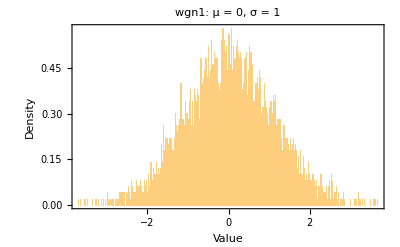

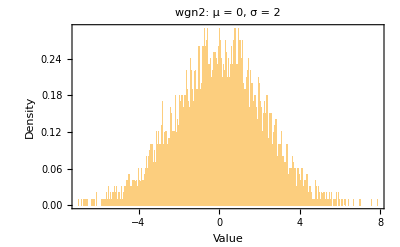

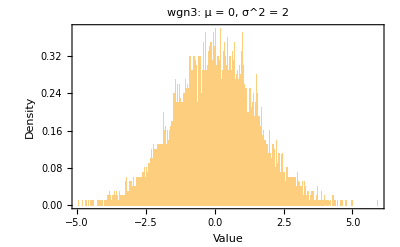

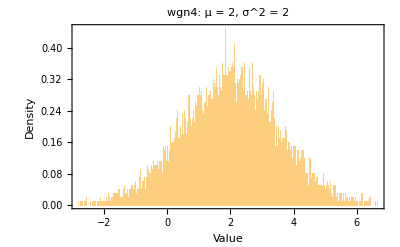

```mathematica
numSamples=10000;
wgn1=RandomVariate[NormalDistribution[0,1],numSamples];

Histogram[wgn1,1000,"PDF",PlotLabel->"wgn1: μ = 0, σ = 1",Frame->True,FrameLabel->{"Value","Density"}]
wgn2=RandomVariate[NormalDistribution[0,2],numSamples];

Histogram[wgn2,1000,"PDF",PlotLabel->"wgn2: μ = 0, σ = 2",Frame->True,FrameLabel->{"Value","Density"}]
wgn3=RandomVariate[NormalDistribution[0,Sqrt[2]],numSamples];

Histogram[wgn3,1000,"PDF",PlotLabel->"wgn3: μ = 0, σ^2 = 2",Frame->True,FrameLabel->{"Value","Density"}]
wgn4=RandomVariate[NormalDistribution[2,Sqrt[2]],numSamples];

Histogram[wgn4,1000,"PDF",PlotLabel->"wgn4: μ = 2, σ^2 = 2",Frame->True,FrameLabel->{"Value","Density"}]
```

## INITIAL LIGO DS PLOT

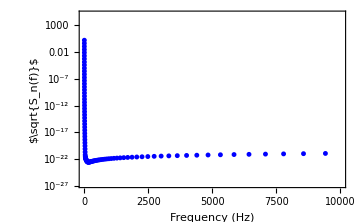

```mathematica
data=Import["C:\\Users\\25095\\Desktop\\DATASCIENCE_COURSE-main\\DATASCIENCE_COURSE-main\\NOISE\\iLIGOSensitivity.txt","Table"];
x=data[[All,1]];
y=data[[All,2]];
ListLogPlot[data,PlotStyle->Blue,PlotMarkers->{{"●",5}},Frame->True,FrameLabel->{"Frequency (Hz)","$\\sqrt{S_n(f)}$"},(*设置坐标轴标签*)GridLines->Automatic,PlotRange->{{0,10000},{10^(-25),10^5}},PlotRangePadding->Scaled[0.05],ImageSize->Medium,(*设置图像大小*)FrameTicksStyle->Directive[FontSize->12],PlotLabel->None ]
```